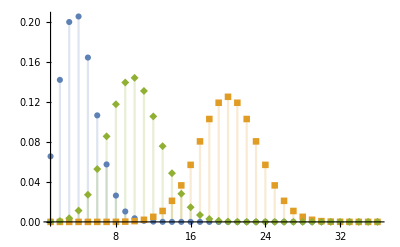

```mathematica
in[1]=DiscretePlot[Table[PDF[BinomialDistribution[40,p],k],{p,{0.1,0.5,0.25}}]//Evaluate,{k,36},PlotRange->All,PlotMarkers->Automatic]
```

```mathematica
in[2]=PDF[BinomialDistribution[n,p],k]
```

Piecewise[{{(1-p)^(-k+n) p^k Binomial[n,k], 0≤k≤n}, {0, True}}]

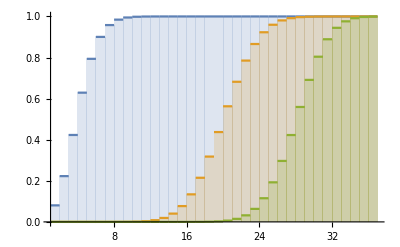

```mathematica
in[4]=DiscretePlot[Table[CDF[BinomialDistribution[40,p],k],{p,{0.1,0.5,0.7}}]//Evaluate,{k,36},ExtentSize->Right]
```

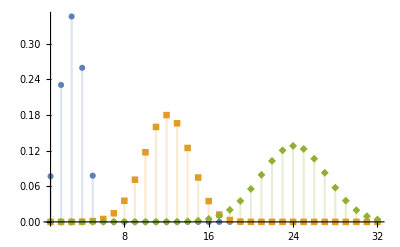

```mathematica
in[5]=DiscretePlot[Table[PDF[BinomialDistribution[n,.6],k],{n,{5,20,40}}]//Evaluate,{k,32},PlotRange->All,PlotMarkers->Automatic]
```

```mathematica
in[6]=PDF[BinomialDistribution[n,p],k]
```

Piecewise[{{(1-p)^(-k+n) p^k Binomial[n,k], 0≤k≤n}, {0, True}}]

WolframAlphaQueryResults

WolframAlphaQueryResults

mean | 40 p
standard deviation | 2 √10 √((1-p) p)
variance | 40 (1-p) p
skewness | (1-2 p)/(2 √10 √((1-p) p))
kurtosis | (1-6 (1-p) p)/(40 (1-p) p)+3